```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];
```

```mathematica
u[𝒸_] := (𝒸^(1-ρ))/(1-ρ);
vFunc[m1_,𝒸1_] := u[𝒸1] + u[m1-𝒸1];
```

```mathematica
ρ = 2;
{𝓂Min,𝓂Mid,𝓂Max}={4,5,6};
{𝒸Min,𝒸Mid,𝒸Max}={𝓂Min,𝓂Mid,𝓂Max}/2;
```

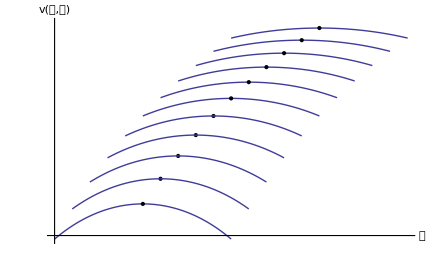

```mathematica
Envelope=Show[
Table[
Show[
Plot[v[𝓂1,𝒸1],{𝒸1,𝓂1/2-.5,𝓂1/2+.5}
,DisplayFunction->Identity
,PlotRange->{{𝒸Min-0.5,𝒸Max+0.5},{vFunc[𝓂Min,𝒸Min-0.5],vFunc[𝓂Max,𝒸Max]+0.01}}
],
Graphics[{PointSize[Medium],Point[{𝓂1/2,vFunc[𝓂1,𝓂1/2]}]}]
],{𝓂1,𝓂Min,𝓂Max,.2}]
,DisplayFunction->$DisplayFunction
,AxesLabel->{"𝒸","v(𝓂,𝒸)"}
,ImageSize->{72. 6., 72. 6./GoldenRatio}
,Ticks->None
]
```

```mathematica
Export["../../Figures/Envelope.pdf",Envelope];
Export["../../Figures/Envelope.png",Envelope,ImageSize->{72. 8.5  ,72. 8.5/GoldenRatio}];(*FullPageSize*)
Export["../../Figures/Envelope.svg",Envelope];
```